## Proof that Monte - Carlo sampling isn' t needed for dilepton emission

```mathematica
nBin=30;
nIter=10^5;
add=0.01;
pdfGamma[x_]:=PDF[GammaDistribution[4,1],x]
```

+0.01 added for visibility

#### If I’m producing dileptons perturbatively (no dynamics associated with them), I can simply oversample (m_ee, q⃗) from a uniform 4D distribution in a large enough range, and weight each dilepton with the value of the distribution function.

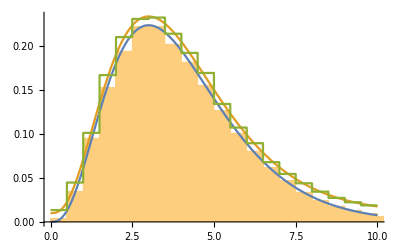

```mathematica
unif=RandomReal[{0,20},nIter];
weight=pdfGamma[#]&/@unif;
dit=HistogramDistribution[WeightedData[unif,weight],nBin];
Show[{Histogram[RandomVariate[GammaDistribution[4,1],nIter],nBin,"PDF",PlotRange->{{0,10},All}],Plot[{pdfGamma[y],pdfGamma[y]+add,PDF[dit,y]+add},{y,0,10},PlotRange->{{0,10},All}]}]
```

#### Actually, we can sample from any arbitrary distribution that has the necessary support, by dividing the weight with the corresponding pdf.

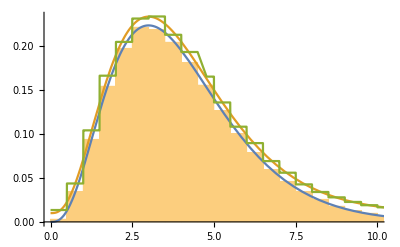

```mathematica
triang=RandomVariate[TriangularDistribution[{0,20},0],nIter];
pdfTriang[x_]:= PDF[TriangularDistribution[{0,20},0],x]
weight=pdfGamma[#]/pdfTriang[#]&/@triang;
dit=HistogramDistribution[WeightedData[triang,weight],nBin];
Show[{Histogram[RandomVariate[GammaDistribution[4,1],nIter],nBin,"PDF",PlotRange->{{0,10},All}],Plot[{pdfGamma[y],pdfGamma[y]+add,PDF[dit,y]+add},{y,0,13},PlotRange->{{0,10},All}]}]
```

#### The beta distribution is defined in the interval [0,1], so it does not have the support we need.

$Aborted

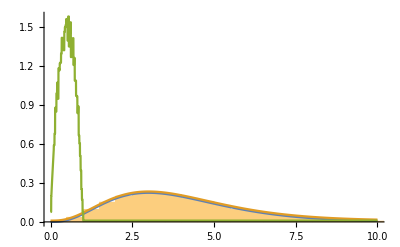

```mathematica
beta=RandomVariate[BetaDistribution[2,2],nIter];
pdfBeta[x_]:= PDF[BetaDistribution[2,2],x]
weight=pdfGamma[#]/pdfBeta[#]&/@beta;
dit=HistogramDistribution[WeightedData[beta,weight],nBin];
Show[{Histogram[RandomVariate[GammaDistribution[4,1],nIter],nBin,"PDF",PlotRange->{{0,10},All}],Plot[{pdfGamma[y],pdfGamma[y]+add,PDF[dit,y]+add},{y,0,10},PlotRange->{{0,10},All}]}]
```